```mathematica
MakeComplete[n1_,n2_,n3_,n4_,n5_]:=Block[{result, currentNode,i,back1, start, highLight},
start=CycleGraph[5];
highLight=EdgeList[start];
result=EdgeAdd[start,1<->6];
result=EdgeAdd[result,2<->6];
result=EdgeAdd[result,2<->7];
result=EdgeAdd[result,3<->7];
result=EdgeAdd[result,3<->8];
result=EdgeAdd[result,4<->8];
result=EdgeAdd[result,4<->9];
result=EdgeAdd[result,5<->9];
result=EdgeAdd[result,5<->10];
result=EdgeAdd[result,1<->10];

currentNode=11;
back1=6; 
For[i=1,i<=n1,i++1,
result=EdgeAdd[result,currentNode<->back1];
result=EdgeAdd[result,currentNode<->1];
back1=currentNode;
currentNode++;
];
result=EdgeAdd[result,back1<->10];
AppendTo[highLight,back1<->10];

back1=10; 
For[i=1,i<=n2,i++1,
result=EdgeAdd[result,currentNode<->back1];
result=EdgeAdd[result,currentNode<->5];
back1=currentNode;
currentNode++;
];
result=EdgeAdd[result,back1<->9];
AppendTo[highLight,back1<->9];

back1=9; 
For[i=1,i<=n3,i++1,
result=EdgeAdd[result,currentNode<->back1];
result=EdgeAdd[result,currentNode<->4];
back1=currentNode;
currentNode++;
];
result=EdgeAdd[result,back1<->8];
AppendTo[highLight,back1<->8];


back1=8; 
For[i=1,i<=n4,i++1,
result=EdgeAdd[result,currentNode<->back1];
result=EdgeAdd[result,currentNode<->3];
back1=currentNode;
currentNode++;
];
result=EdgeAdd[result,back1<->7];
AppendTo[highLight,back1<->7];

back1=7; 
For[i=1,i<=n5,i++1,
result=EdgeAdd[result,currentNode<->back1];
result=EdgeAdd[result,currentNode<->2];
back1=currentNode;
currentNode++;
];
result=EdgeAdd[result,back1<->6];
AppendTo[highLight,back1<->6];

Graph[result,VertexLabels->"Name", GraphHighlight->highLight]
]
```

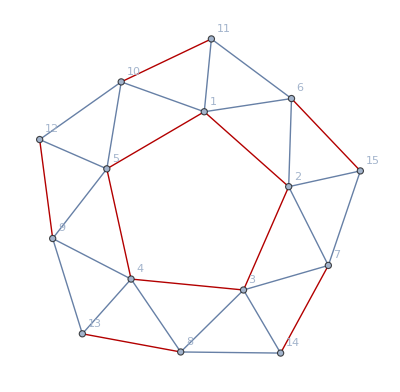

```mathematica
g=Graph[MakeComplete[1,1,1,1,1],GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
PerMatrixCount[MakeComplete[1,1,1,1,1],{1<->3,1<->4},{2<->4,2<->5},{3<->5}]
```

$Aborted

```mathematica
PerMatrixCount[PetersenGraph[],{1<->3,1<->4},{2<->4,2<->5},{3<->5}]
```

{{{1,2,3},1080}}

```mathematica
PlanarGraphQ[PetersenGraph[]]
```

False

```mathematica
PerMatrixCount[EdgeAdd[CycleGraph[5],Table[i<->6,{i,1,5}]],{1<->3,1<->4},{2<->4,2<->5},{3<->5}]
```

{{{1},2},{{2},2},{{3},6}}

```mathematica
PerMatrix3[EdgeAdd[CycleGraph[5],Flatten[Table[i<->6,{i,1,5}],1]],{1<->3,1<->4},{2<->4,2<->5},{3<->5}]
```

{{{1},2},{{2},2},{{3},6}}

{{1}→-Graphics-,{1}→-Graphics-,{2}→-Graphics-,{2}→-Graphics-,{3}→-Graphics-,{3}→-Graphics-,{3}→-Graphics-,{3}→-Graphics-,{3}→-Graphics-,{3}→-Graphics-}